```mathematica
res=(Series[(2 rm)/(r √((1-um^2)r^2- rm^2(1-um^2 u^(2α))))/.{u->rm/r},{um,0,2}]//Normal)//ExpandAll
```

(2 rm)/(r √(r^2-rm^2))+(r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)/.{α->1/2}
int = Integrate[%,r]
Limit[int,r->rm]
Limit[int/.{rm->1},r->∞]
Limit[int/.{rm->1},r->∞]//N
```

(rm (r^2-rm^3/r) um^2)/(r ((r-rm) (r+rm))^(3/2))

((2 r^2-r rm-rm^2) um^2)/(r √(r^2-rm^2))

0

2 um^2

2. um^2

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)/.{α->1}
int = Integrate[%,r]
Limit[int,r->rm]
Limit[int/.{rm->1},r->∞]
Limit[int/.{rm->1},r->∞]//N
```

(rm (r^2-rm^4/r^2) um^2)/(r ((r-rm) (r+rm))^(3/2))

1/2 rm um^2 ((√(r^2-rm^2))/r^2+(3 ArcTan[(√(r^2-rm^2))/rm])/rm)

0

(3 π um^2)/4

2.35619 um^2

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)/.{α->1.5}
int = Integrate[%,r]
Limit[int,r->rm]
Limit[int/.{rm->1},r->∞]
Limit[int/.{rm->1},r->∞]//N
```

(rm (r^2-rm^2 (rm/r)^3.) um^2)/(r ((r-rm) (r+rm))^(3/2))

(rm (-1. (r^2-1. rm^2)-(2.66667 (1.-(1. r^2)/rm^2)^1. (rm/r)^3. (1. r^4-0.5 r^2 rm^2-0.125 rm^4))/rm^2.) um^2)/((r^2-1. rm^2)^(3/2))

ConditionalExpression[0., um^2∈ℝ&&rm>0]

2.66667 um^2

2.66667 um^2

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)/.{α->2}
int = Integrate[%,r]
Limit[int,r->rm]
Limit[int/.{rm->1},r->∞]
Limit[int/.{rm->1},r->∞]//N
```

(rm (r^2-rm^6/r^4) um^2)/(r ((r-rm) (r+rm))^(3/2))

1/8 rm um^2 ((√(r^2-rm^2) (7 r^2+2 rm^2))/r^4+(15 ArcTan[(√(r^2-rm^2))/rm])/rm)

0

(15 π um^2)/16

2.94524 um^2

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)/.{α->1/2}
int = Integrate[%,r]
Limit[int,r->rm]
Limit[int/.{rm->1},r->∞]
Limit[int/.{rm->1},r->∞]//N
```

(rm (r^2-rm^3/r) um^2)/(r ((r-rm) (r+rm))^(3/2))

((2 r^2-r rm-rm^2) um^2)/(r √(r^2-rm^2))

0

2 um^2

2. um^2

```mathematica
((r^2 rm um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))-(rm^3 (rm/r)^(2 α) um^2)/(r^3 √(r^2-rm^2)-r rm^2 √(r^2-rm^2))//FullSimplify)
int = Integrate[%,r]
```

(rm (r^2-rm^2 (rm/r)^(2 α)) um^2)/(r ((r-rm) (r+rm))^(3/2))

(rm um^2 (-2 α-√(1-r^2/rm^2) (rm/r)^(2 α) Hypergeometric2F1[3/2,-α,1-α,r^2/rm^2]))/(2 √(r^2-rm^2) α)

```mathematica
Limit[D[Hypergeometric2F1[3/2,-α,1-α,x],{x,2}]//FullSimplify,x->1]
```

Indeterminate

```mathematica
Limit[D[1/√(x-1),{x,2}],{x->1}]
```

Indeterminate

```mathematica
√(rm^2-r^2)/√(r^2-rm^2)//FullSimplify
```

(√(-r^2+rm^2))/(√((r-rm) (r+rm)))

```mathematica
Gamma[1-α-3/2]
```

Gamma[-1/2-α]

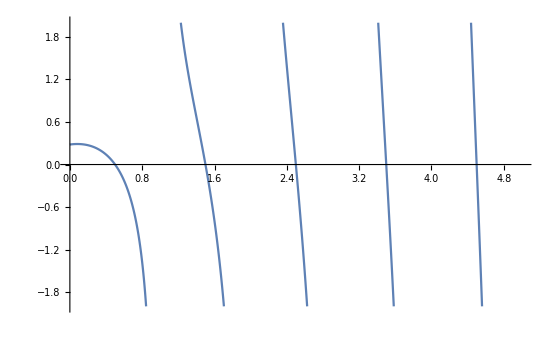

```mathematica
Plot[-Gamma[1-α]/Gamma[-1/2-α],{α,0,5},PlotRange->{-2,2},PlotPoints->2000,GridLines->{{1/2,3/2,5/2,7/2,9/2},{}}]
```